```mathematica
v004=-0.04Exp[2Pi I {{1,0},{-1,0},{0,1},{0,-1}}.{x,0}]//Total
```

-0.08-0.04 ⅇ^(-2 ⅈ π x)-0.04 ⅇ^(2 ⅈ π x)

```mathematica
v002=-0.02Exp[2Pi I {{1,1},{-1,-1},{-1,1},{1,-1}}.{x,0}]//Total
```

-0.04 ⅇ^(-2 ⅈ π x)-0.04 ⅇ^(2 ⅈ π x)

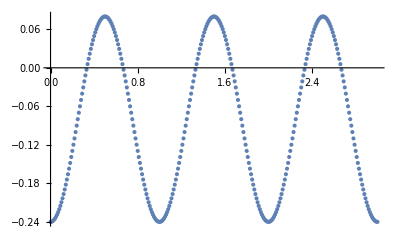

```mathematica
ListPlot[Table[{x,v004+v002//Re},{x,0,3,0.01}],PlotRange->All]
```

```mathematica
0 + v004+v002//FullSimplify
```

-0.08-0.16 Cos[2 π x]